1.10322

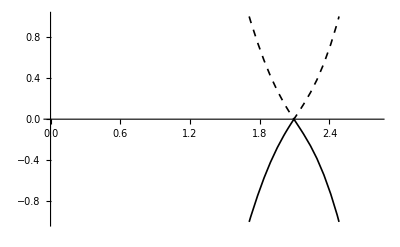

```mathematica
Clear["Global`*"]
L1=1; m1=3*√3; L2=0.1;
g1={{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}};
g2={{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}};
g12={{0,I,0,0},{-I,0,0,0},{0,0,0,I},{0,0,-I,0}};
g15={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}};
d1[x_,y_]=1+2*Cos[y]*Cos[x];
d12[x_,y_]=2*Sin[y]*Cos[x];
d15[x_,y_]=-4*Sin[x]*Cos[y]+2*Sin[2*x];
d3[x_,y_]=(1-Cos[x]*Cos[y])*L2;
d23[x_,y_]=-Cos[x]*Sin[y]*L2;
d4[x_,y_]=-√3*Sin[x]*Sin[y]*L2;
d24[x_,y_]=√3*Sin[x]*Sin[y]*L2;
M11=d1[x,y]*g1+g2*m1+g12*d12[x,y]+g15*d15[x,y]*L1;
M1={{m1+L1*d15[x,y],d1[x,y]+I*d12[x,y],0,-I*d3[x,y]-d4[x,y]+d23[x,y]+I*d24[x,y]},{d1[x,y]-I*d12[x,y],-(m1+L1*d15[x,y]),I*d3[x,y]+d4[x,y]+d23[x,y]+I*d24[x,y],0},{0,-I*d3[x,y]+d4[x,y]+d23[x,y]-I*d24[x,y],m1-L1*d15[x,y],d1[x,y]+I*d12[x,y]},{-d4[x,y]+I*d3[x,y]+d23[x,y]-I*d24[x,y],0,d1[x,y]-I*d12[x,y],-(m1-L1*d15[x,y])}};
A=Eigenvalues[M11];
F1[x_,y_]=A[[1]]; F2[x_,y_]=A[[2]]; F3[x_,y_]=A[[3]];F4[x_,y_]=A[[4]];
2*√3/3.14
Plot[{F1[x,0],F2[x,0],F3[x,0],F4[x,0]},{x,0,5.1*√3/3.14},PlotRange->{-1,1}, PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Green},{Thickness[0.003],Green, Dashed}}]
```

```mathematica
x=Pi/3; y=Pi;
B=Eigenvectors[M1];
V1=B[[1]]; V2=B[[2]]; V3=B[[3]];V4=B[[4]];
T={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
V11=Conjugate[B[[1]]];V22=Conjugate[B[[2]]];V33=Conjugate[B[[3]]];V44=Conjugate[B[[4]]];
G1=T.V11;G2=T.V22;G3=T.V33;G4=T.V44;
P12=V11.G3
```

0.+0. ⅈ